### Mass Matrix - 1 Flavour Scenario for Completely Non-local Clockwork

```mathematica
K = 15;a=1;
(* qt is q^∼ (Majorana mass term), K is the number of sites and a is mass term (m) cw fermions. *)
```

```mathematica
(*Clear[q];Clear[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16,a17,a18,a19,a20]*)
```

```mathematica
list = Table[-5,{i,K}]; (*A list to store coupling strength parameter values for next to nearest neighbour and so on which is 5 in this case.*)
```

```mathematica
CNCW = Table[0,{x,K},{y,K+1}];
```

```mathematica
j=1;
While[j<K+1,{i=j;While[i<K+2,{CNCW[[j,i]] = list[[-j+i]]};i++]};j++]
i=1;While[i<K+1,{CNCW[[i,i]] = a};i++](* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
```

```mathematica
CNCW
```

(1 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5
0 | 1 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5
0 | 0 | 1 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5
0 | 0 | 0 | 1 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5
0 | 0 | 0 | 0 | 1 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5
0 | 0 | 0 | 0 | 0 | 1 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5
0 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | -5 | -5 | -5 | -5 | -5 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | -5 | -5 | -5 | -5 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | -5 | -5 | -5 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | -5 | -5 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | -5 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -5)

```mathematica
Rw = Transpose[CNCW].CNCW;
```

```mathematica
N[Eigenvalues[Rw],30] (*30 digits of precision.*)
```

{2379.96433168194932179263863711,271.682157144859697796163293297,103.03706132148307958807465775,56.5963323760687072787267442373,37.5113049106697509013581750747,27.8799668829969870762039249918,22.3729589406194859896436127688,18.9533624386450485169653276282,16.706971367041707744197475376,15.1747570635485877475364676588,14.1065969652068096825676193445,13.3577947870023622672522648151,12.8411750075916353093161682784,12.5032712332239965448322488872,12.3119578790928217645233827817,0}

```mathematica
Eigenvectors[N[Rw,30]];
```

```mathematica
zr = Table[0,{i,1,K},{j,1,K}];
zr1 = Table[0,{i,1,K+1},{j,1,K+1}];
```

```mathematica
Mt = ArrayFlatten[{{zr,CNCW},{Transpose[CNCW],zr1}}];
```

```mathematica
ns =N[NullSpace[N[Mt,30]],30]
```

(1.90158977013785718589099997151×10^-54 | -1.67366972544091930074265881596×10^-51 | 3.72535805056537481940651929336×10^-50 | -4.15628549103644714727348526159×10^-49 | 3.03520024335347189824817525178×10^-48 | -1.61550494006546749759486918319×10^-47 | 6.63622896107150623759113653437×10^-47 | -2.17758071779693243644004289301×10^-46 | 5.83278163676368655477801181949×10^-46 | -1.29223701489353436661120571128×10^-45 | 2.38272119271485549429678055099×10^-45 | -3.65206378367638648442376636271×10^-45 | 4.59624319836456646850641118326×10^-45 | -4.58342466561366404658290209461×10^-45 | 3.24332755112841070070161282339×10^-45 | 0.986013297183269340427887156572 | 0.164335549530544890071314526095 | 0.0273892582550908150118857543492 | 0.00456487637584846916864762572487 | 0.000760812729308078194774604287479 | 0.000126802121551346365795767381246 | 0.0000211336869252243942992945635411 | 3.52228115420406571654909392351×10^-6 | 5.87046859034010952758182320585×10^-7 | 9.78411431723351587930303867642×10^-8 | 1.63068571953891931321717311274×10^-8 | 2.71780953256486552202862185456×10^-9 | 4.52968255427477587004770309094×10^-10 | 7.54947092379129311674617181823×10^-11 | 1.25824515396521551945769530303×10^-11 | 2.5164903079304310389153906059×10^-12)

```mathematica
ev = Eigenvalues[N[Mt,30]]
```

{-48.7848781046130043704194356467,48.7848781046130043704194356467,16.4827836588623493889523344137,-16.4827836588623493889523344137,-10.1507172811325545058817743982,10.1507172811325545058817743982,-7.52305339447147000499571758534,7.52305339447147000499571758534,-6.12464732949332772447988921837,6.12464732949332772447988921837,-5.2801483769868614437616354479,5.2801483769868614437616354479,-4.73000623050535589774352455614,4.73000623050535589774352455614,4.35354596147152769633330503155,-4.35354596147152769633330503155,4.08741622140952361125223486114,-4.08741622140952361125223486114,-3.89547905443587101666732310912,3.89547905443587101666732310912,-3.75587499328808994408997673589,3.75587499328808994408997673589,-3.65483170433364308518936760142,3.65483170433364308518936760142,-3.58345852600412208388932129737,3.58345852600412208388932129737,-3.53599649790889874190479888988,3.53599649790889874190479888988,-3.50883996202346364073398458394,3.50883996202346364073398458394,2.07548567688514862828572397536×10^-58}

```mathematica
Kcw =CNCW;
```

```mathematica
{s1,s2,s3}=SingularValueDecomposition[N[Kcw,30]];
```

```mathematica
Y = N[Eigenvectors[N[Mt,30]],30];
```

```mathematica
H= Inverse[N[Y,30]];
```

```mathematica
Ev1 = Sort[Abs[ ev]];
```

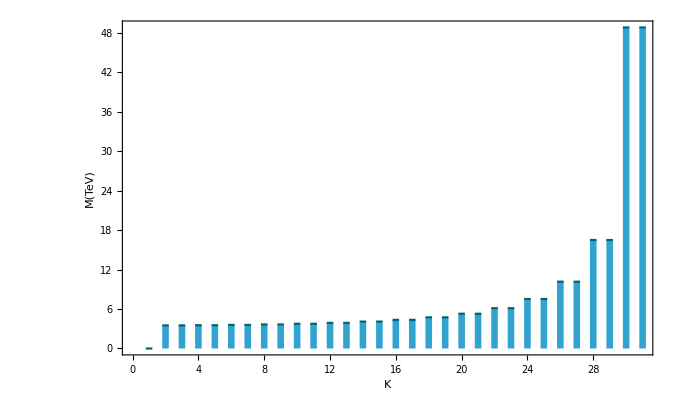

```mathematica
DiscretePlot[Ev1⟦i⟧,{i,1,2 K+1},PlotStyle->Directive[RGBColor[0.,0.4,0.42],Opacity[1.],AbsoluteThickness[1.545]],ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,0.6,0.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"K","M(TeV)"},LabelStyle->Directive[Bold,Medium],PlotRange->{0,All}, Epilog->{Text[ "",Scaled[{0.8,0.95}]],Text["",Scaled[{0.8,0.9}]]}]
```

```mathematica
Rn = H[[2K+1,All]] 
(* Change of basis from Subscript[ψ^c, R,r]  to eigenvector of cw2 in interaction term. *)
```

{-0.255207078270468615967028903909,0.255207078270468615967028903909,-0.251689266284079574572864293909,-0.251689266284079574572864293909,-0.24497816494424381459811147766,0.24497816494424381459811147766,0.235617448377202492054358136051,-0.235617448377202492054358136051,0.224212854758417098163375484921,-0.224212854758417098163375484921,-0.211288917284821576218640085891,0.211288917284821576218640085891,0.197197303585298881497827607088,-0.197197303585298881497827607088,0.182079793872442275500957763534,0.182079793872442275500957763534,0.165871147147304013979244407045,-0.165871147147304013979244407045,0.148328330050140908068185245642,0.148328330050140908068185245642,-0.129083895429091504182795760757,-0.129083895429091504182795760759,0.107733191385536312444918297032,-0.107733191385536312444918297035,-0.0839678693334309015824040971199,-0.0839678693334309015824040971199,0.0577494986328728418033721611484,-0.0577494986328728418033721611484,-0.0294704473178355047748794814808,-0.0294704473178355047748794814808,-2.51649030793043103891539060608×10^-12}

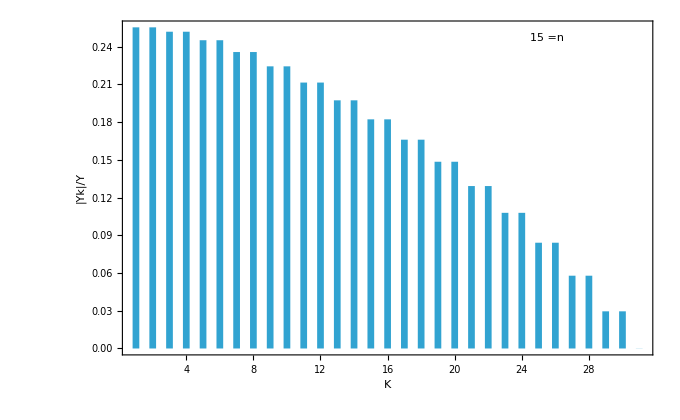

```mathematica
DiscretePlot[Abs[Rn[[i]]],{i,1,2*K+1},ExtentSize->0.4,ImageSize->680,PlotRange->All,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"K","|Yk|/Y"},LabelStyle->Directive[Bold, Medium],Epilog->{Text["",Scaled[{0.8,0.90}]],Text["",Scaled[{0.8,0.95}]],{Text[K"=n",Scaled[{.8,.95}]]}}]
```

```mathematica
Lvector = Transpose[s1];(*Left Eigenvector of NNNCW*)
Rvector= Transpose[s3];(*Right Eigenvector of NNNCW*)
```

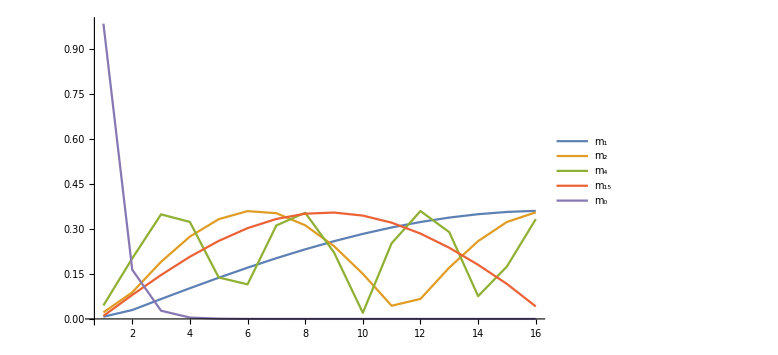
-Graphics-Absolute value of eigenvector componentsSite

```mathematica
Labeled[Labeled[ListLinePlot[{Abs[Rvector[[1]]],Abs[Rvector[[2]]],Abs[Rvector[[4]]],Abs[Rvector[[15]]],Abs[Rvector[[-1]]]},PlotRange->All,PlotLegends->Placed[LineLegend[ColorData[97]/@Range[Length[Rvector]],(*Explicit colors*){"\!\(\*SubscriptBox[\(m\), \(1\)]\)","\!\(\*SubscriptBox[\(m\), \(2\)]\)","\!\(\*SubscriptBox[\(m\), \(4\)]\)","m_15","\!\(\*SubscriptBox[\(m\), \(0\)]\)"}]//Framed[#,FrameStyle->Black,RoundingRadius->5,Background->White]&,Right],AxesLabel->{None,None},PlotRange->All,ImageSize->Large,PlotStyle->ColorData[97]/@Range[Length[Rvector]]],Style[Rotate["Absolute value of eigenvector components",90 Degree],14],Left],Style["Site",14],Bottom]
```

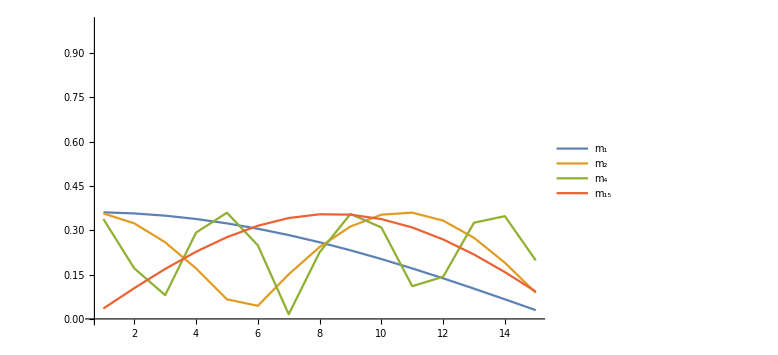
-Graphics-Absolute value of eigenvector componentsSite

```mathematica
Labeled[Labeled[ListLinePlot[{Abs[Lvector[[1]]],Abs[Lvector[[2]]],Abs[Lvector[[4]]],Abs[Lvector[[15]]]},PlotRange->{All,{0,1}},PlotLegends->Placed[LineLegend[ColorData[97]/@Range[Length[Rvector]],(*Explicit colors*){"\!\(\*SubscriptBox[\(m\), \(1\)]\)","\!\(\*SubscriptBox[\(m\), \(2\)]\)","\!\(\*SubscriptBox[\(m\), \(4\)]\)","m_15"}]//Framed[#,FrameStyle->Black,RoundingRadius->5,Background->White]&,Right],AxesLabel->{None,None},PlotRange->All,ImageSize->Large,PlotStyle->ColorData[97]/@Range[Length[Rvector]]],Style[Rotate["Absolute value of eigenvector components",90 Degree],14],Left],Style["Site",14],Bottom]
```

### 3 Flavour Scenario

```mathematica
K=15;v=0.173;p=0.1*v;
(*K is the number of sites parameter, p is the coupling strength between SM neutrino and Subscript[R, n].*)
```

```mathematica
cw= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form clockwork mass matrix *)
```

```mathematica
list=Table[-5,{i,1,K}](*A list to store coupling strength parameter values for next to nearest neighbour and so on which is 5 in this case.*)
```

{-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5,-5}

```mathematica
j=1;
While[j<K+3,{i=1;While[i<K-j+2,{cw[[i+j,i]] = list[[j]]};i++]};j++]
i=1;While[i<K+1,{cw[[i+1,i+1]] = 1};i++]
cw2=cw;cw3=cw;
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
```

```mathematica
cw[[1,1]]=1.386p;cw2[[1,1]]=1.4p;cw3[[1,1]]=0.8p; (*3 CN-CW chains for 3 masses.*)
```

```mathematica
cw3
```

(0.01384 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1 | 0
-5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | -5 | 1)

```mathematica
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[cw,20]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[cw2,20]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[cw3,20]];
```

```mathematica
a1=m1[[-1,-1]]
a2=m2[[-1,-1]]
a3=m3[[-1,-1]](*Three Masses produced*)
```

6.0339405718532906458×10^-14

6.0948884501249142095×10^-14

3.4828130559385200781×10^-14

```mathematica
(a2^2-a1^2)*Power[10,24](*Mass squared differences Subscript[Δm^2, 21].*)
(a3^2-a2^2)*Power[10,24](*Mass squared differences Subscript[Δm^2, 32].*)
```

0.000073922639480886271

-0.002501767843685026586